```mathematica
ClearAll["Global`*"];
MatrixForm[FullSimplify[Limit[MatrixPower[EulerMatrix[{φ/s,θ/s,ψ/s}],s*t],s->Infinity]]]
MatrixForm[FullSimplify[Limit[MatrixPower[EulerMatrix[{φ*t/s,θ*t/s,ψ*t/s}],s],s->Infinity]]]
```

(Cosh[t √(-θ^2-(φ+ψ)^2)] | -((φ+ψ) Sinh[t √(-θ^2-(φ+ψ)^2)])/(√(-θ^2-(φ+ψ)^2)) | (θ Sinh[t √(-θ^2-(φ+ψ)^2)])/(√(-θ^2-(φ+ψ)^2))
((φ+ψ) Sinh[t √(-θ^2-(φ+ψ)^2)])/(√(-θ^2-(φ+ψ)^2)) | (θ^2+(φ+ψ)^2 Cosh[t √(-θ^2-(φ+ψ)^2)])/(θ^2+(φ+ψ)^2) | -(θ (φ+ψ) (-1+Cosh[t √(-θ^2-(φ+ψ)^2)]))/(θ^2+(φ+ψ)^2)
-(θ Sinh[t √(-θ^2-(φ+ψ)^2)])/(√(-θ^2-(φ+ψ)^2)) | -(θ (φ+ψ) (-1+Cosh[t √(-θ^2-(φ+ψ)^2)]))/(θ^2+(φ+ψ)^2) | ((φ+ψ)^2+θ^2 Cosh[t √(-θ^2-(φ+ψ)^2)])/(θ^2+(φ+ψ)^2))

(Cosh[√(-t^2 (θ^2+(φ+ψ)^2))] | -(t (φ+ψ) Sinh[√(-t^2 (θ^2+(φ+ψ)^2))])/(√(-t^2 (θ^2+(φ+ψ)^2))) | (t θ Sinh[√(-t^2 (θ^2+(φ+ψ)^2))])/(√(-t^2 (θ^2+(φ+ψ)^2)))
(t (φ+ψ) Sinh[√(-t^2 (θ^2+(φ+ψ)^2))])/(√(-t^2 (θ^2+(φ+ψ)^2))) | (θ^2+(φ+ψ)^2 Cosh[√(-t^2 (θ^2+(φ+ψ)^2))])/(θ^2+(φ+ψ)^2) | -(θ (φ+ψ) (-1+Cosh[√(-t^2 (θ^2+(φ+ψ)^2))]))/(θ^2+(φ+ψ)^2)
-(t θ Sinh[√(-t^2 (θ^2+(φ+ψ)^2))])/(√(-t^2 (θ^2+(φ+ψ)^2))) | -(θ (φ+ψ) (-1+Cosh[√(-t^2 (θ^2+(φ+ψ)^2))]))/(θ^2+(φ+ψ)^2) | ((φ+ψ)^2+θ^2 Cosh[√(-t^2 (θ^2+(φ+ψ)^2))])/(θ^2+(φ+ψ)^2))

```mathematica
SP[t_,θ_,ϕ_,ψ_]:={{Cosh[t Sqrt[-θ^2-(ϕ+ψ)^2]],-((ϕ+ψ) Sinh[t Sqrt[-θ^2-(ϕ+ψ)^2]]/Sqrt[-θ^2-(ϕ+ψ)^2]),(θ Sinh[t Sqrt[-θ^2-(ϕ+ψ)^2]])/Sqrt[-θ^2-(ϕ+ψ)^2]},{((ϕ+ψ) Sinh[t Sqrt[-θ^2-(ϕ+ψ)^2]])/Sqrt[-θ^2-(ϕ+ψ)^2],(θ^2+(ϕ+ψ)^2 Cosh[t Sqrt[-θ^2-(ϕ+ψ)^2]])/(θ^2+(ϕ+ψ)^2),-((θ (ϕ+ψ) (-1+Cosh[t Sqrt[-θ^2-(ϕ+ψ)^2]]))/(θ^2+(ϕ+ψ)^2))},{-((θ Sinh[t Sqrt[-θ^2-(ϕ+ψ)^2]])/Sqrt[-θ^2-(ϕ+ψ)^2]),-((θ (ϕ+ψ) (-1+Cosh[t Sqrt[-θ^2-(ϕ+ψ)^2]]))/(θ^2+(ϕ+ψ)^2)),((ϕ+ψ)^2+θ^2 Cosh[t Sqrt[-θ^2-(ϕ+ψ)^2]])/(θ^2+(ϕ+ψ)^2)}};
J = MatrixForm[FullSimplify[D[SP[t, θ,ϕ,ψ],t]/. t->0]]
Eigenvalues[FullSimplify[D[SP[t, θ,ϕ,ψ],t]/. t->0]]
```

(0 | -ϕ-ψ | θ
ϕ+ψ | 0 | 0
-θ | 0 | 0)

{0,-√(-θ^2-ϕ^2-2 ϕ ψ-ψ^2),√(-θ^2-ϕ^2-2 ϕ ψ-ψ^2)}

Analyzing Case 1: All equal

Max Elevation Error: 1.7630229413184133654

Max Azimuthal Error: 3.1415926535867888414

Min Elevation Error: 4.9940027423149439502×10^-11

Min Azimuthal Error: 6.4183533624747516461×10^-11

Elevation Error Period: 40 √5

Azimuthal Error Period: 40 √5

Elevation Error Plot (Max):

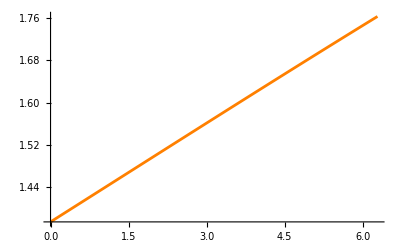

Azimuthal Error Plot (Max):

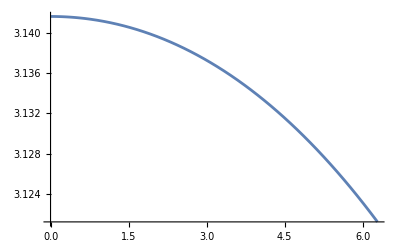

Elevation Error Plot (Min):

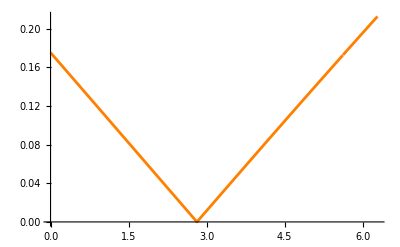

Azimuthal Error Plot (Min):

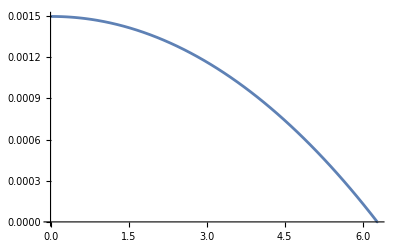

Analyzing Case 2: Rational ratios

Max Elevation Error: 1.76728544886722705

Max Azimuthal Error: 3.1415926535847018503

Min Elevation Error: 3.8720978798019742804×10^-13

Min Azimuthal Error: 2.2447258825688013756×10^-10

Elevation Error Period: 1200/(√61)

Azimuthal Error Period: 1200/(√61)

Elevation Error Plot (Max):

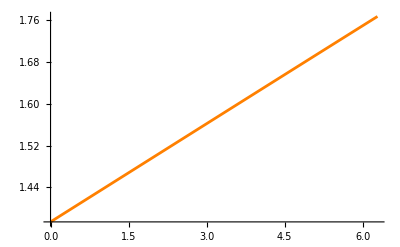

Azimuthal Error Plot (Max):

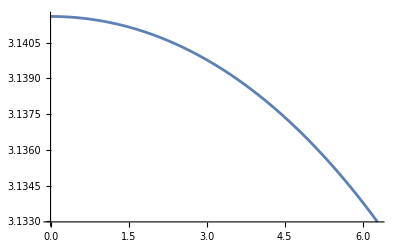

Elevation Error Plot (Min):

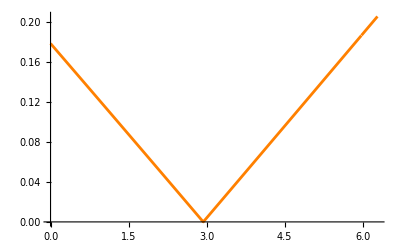

Azimuthal Error Plot (Min):

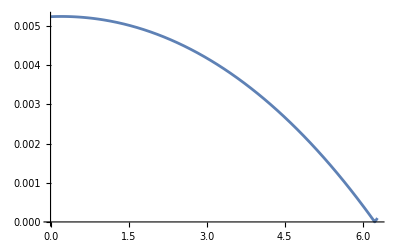

Analyzing Case 3: Two equal, rational ratio

NMinimize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

Max Elevation Error: 1.7045487138639725845

Max Azimuthal Error: 3.1415926535887034985

Min Elevation Error: 3.0551342654246962055×10^-12

Min Azimuthal Error: 2.1008834002918577286×10^-10

Elevation Error Period: 400/(√13)

Azimuthal Error Period: 400/(√13)

Elevation Error Plot (Max):

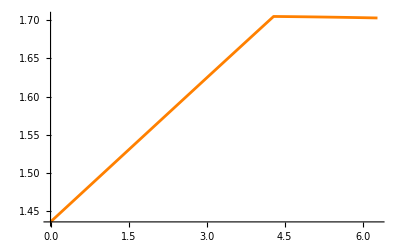

Azimuthal Error Plot (Max):

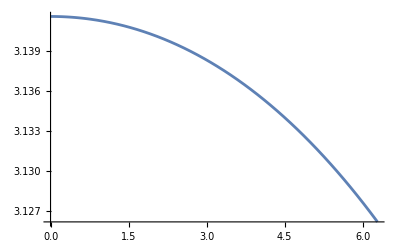

Elevation Error Plot (Min):

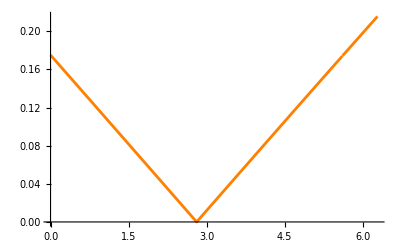

Azimuthal Error Plot (Min):

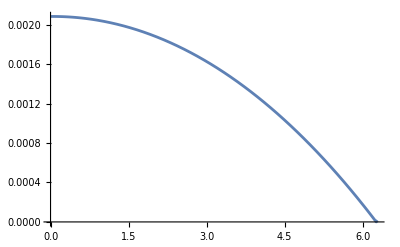

Analyzing Case 4: Irrational ratios

Max Elevation Error: 2.0731745488505802829

Max Azimuthal Error: 3.141592653589768069

Min Elevation Error: 2.1826078194734911042×10^-12

Min Azimuthal Error: 5.4753960043942458876×10^-11

Elevation Error Period: (2 π)/(√(9+6 ⅇ+ⅇ^2+π^2))

Azimuthal Error Period: (2 π)/(√(9+6 ⅇ+ⅇ^2+π^2))

Elevation Error Plot (Max):

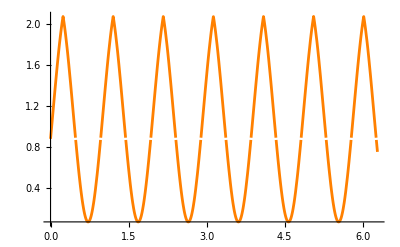

Azimuthal Error Plot (Max):

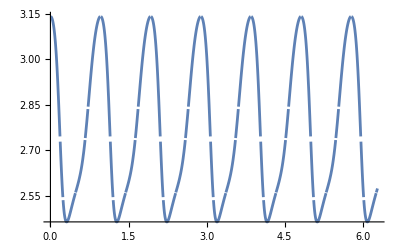

Elevation Error Plot (Min):

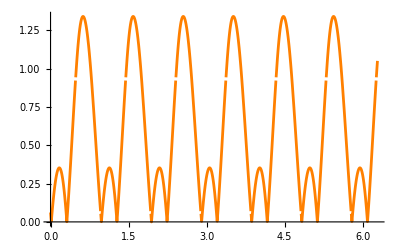

Azimuthal Error Plot (Min):

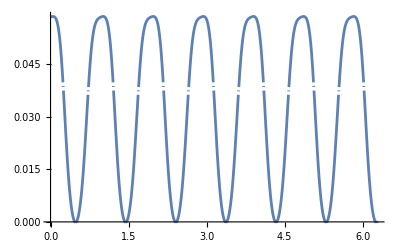

Analyzing Case 5: Two equal, irrational ratio

Max Elevation Error: 1.5594622273775664873

Max Azimuthal Error: 3.1415926535887663273

Min Elevation Error: 1.6852804384192267065×10^-12

Min Azimuthal Error: 3.1882777760665249724×10^-10

Elevation Error Period: 100 π √(2/(5000 ⅇ^2+100 ⅇ π+π^2))

Azimuthal Error Period: 100 π √(2/(5000 ⅇ^2+100 ⅇ π+π^2))

Elevation Error Plot (Max):

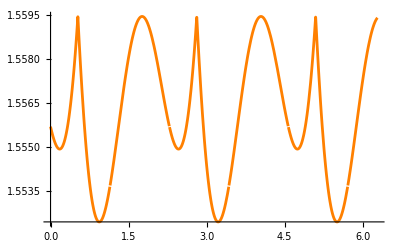

Azimuthal Error Plot (Max):

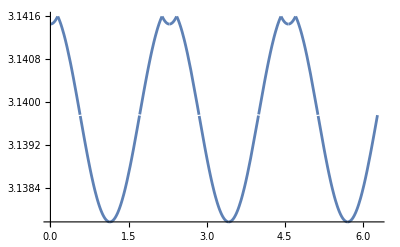

Elevation Error Plot (Min):

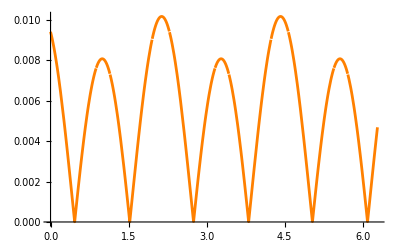

Azimuthal Error Plot (Min):

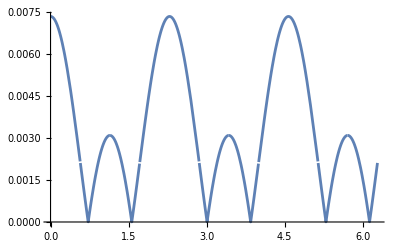

Analyzing Case 1: All equal - Eldar's Case

NMinimize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

Max Elevation Error: 2.0344438977266328844

Max Azimuthal Error: 3.1415926535778856311

Min Elevation Error: 3.4588220574783460724×10^-11

Min Azimuthal Error: 2.3135942471700615471×10^-10

Elevation Error Period: (2 π)/(√5)

Azimuthal Error Period: (2 π)/(√5)

Elevation Error Plot (Max):

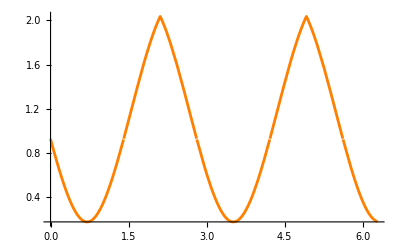

Azimuthal Error Plot (Max):

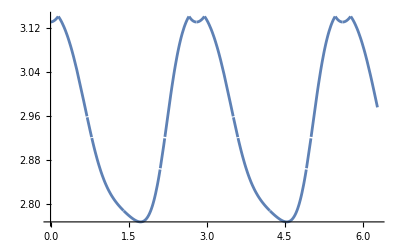

Elevation Error Plot (Min):

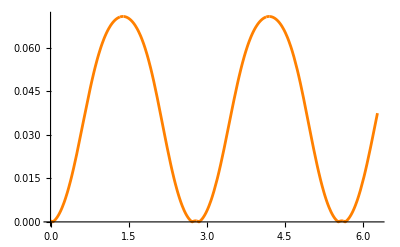

Azimuthal Error Plot (Min):

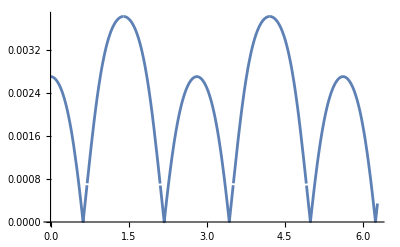

Analyzing Case 2: Rational ratios - Subcase 1

Max Elevation Error: 1.7681881882204978909

Max Azimuthal Error: 3.141592653584863579

Min Elevation Error: 1.3979472146213600247×10^-11

Min Azimuthal Error: 1.9474154031478627711×10^-12

Elevation Error Period: √(2/13) π

Azimuthal Error Period: √(2/13) π

Elevation Error Plot (Max):

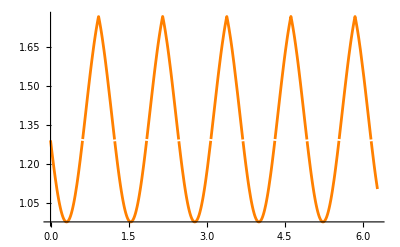

Azimuthal Error Plot (Max):

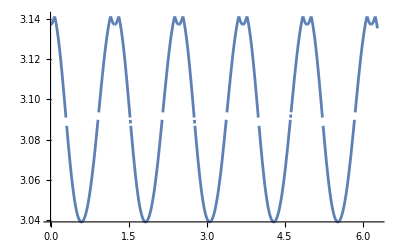

Elevation Error Plot (Min):

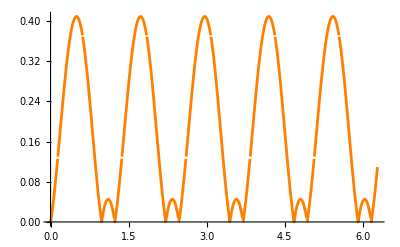

Azimuthal Error Plot (Min):

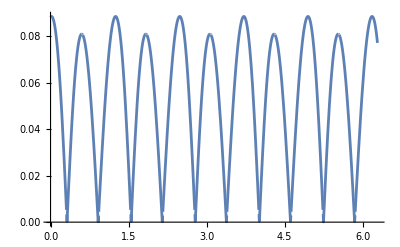

Analyzing Case 2: Rational ratios - Subcase 2

NMinimize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

Max Elevation Error: 2.3559058666492491839

Max Azimuthal Error: 3.1415926535893405832

Min Elevation Error: 0

Min Azimuthal Error: 3.000272238420892201×10^-10

Elevation Error Period: (√2 π)/3

Azimuthal Error Period: (√2 π)/3

Elevation Error Plot (Max):

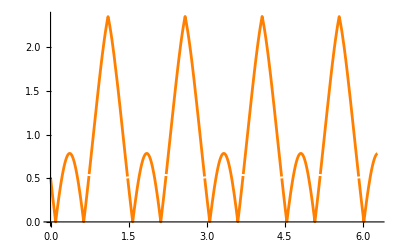

Azimuthal Error Plot (Max):

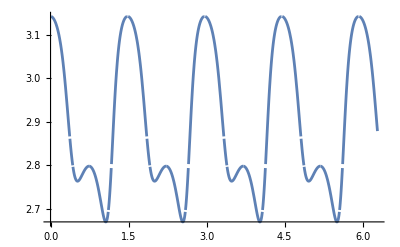

Elevation Error Plot (Min):

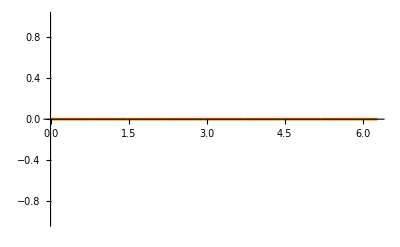

Azimuthal Error Plot (Min):

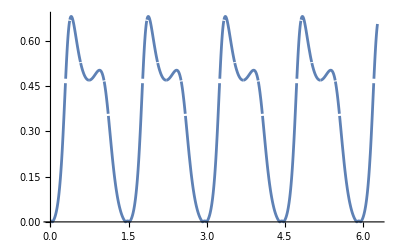

Analyzing Case 3: Two equal, rational ratio - Subcase 1

NMinimize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

Max Elevation Error: 1.570796326709863653

Max Azimuthal Error: 3.1415926535894283527

Min Elevation Error: 2.2670063914131539697×10^-12

Min Azimuthal Error: 8.4088603622626060873×10^-11

Elevation Error Period: √(2/5) π

Azimuthal Error Period: √(2/5) π

Elevation Error Plot (Max):

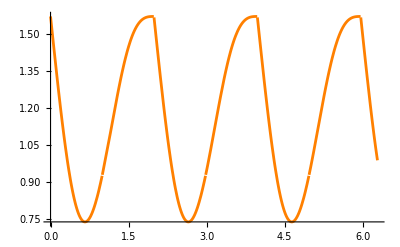

Azimuthal Error Plot (Max):

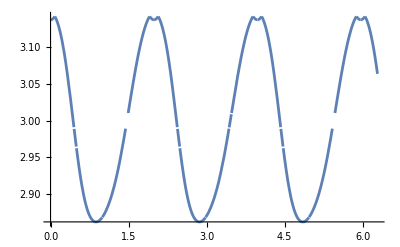

Elevation Error Plot (Min):

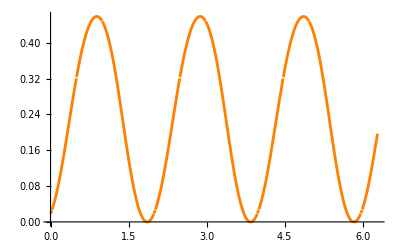

Azimuthal Error Plot (Min):

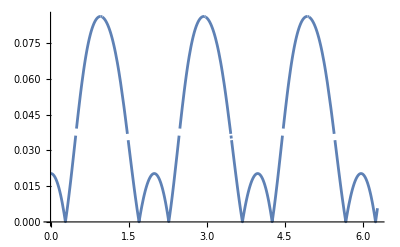

Analyzing Case 3: Two equal, rational ratio - Subcase 2

NMinimize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

Max Elevation Error: 2.3561944841605743135

Max Azimuthal Error: 3.1415926535761123302

Min Elevation Error: 7.0219503177851989711×10^-11

Min Azimuthal Error: 2.0835503096934410769×10^-10

Elevation Error Period: π/(√2)

Azimuthal Error Period: π/(√2)

Elevation Error Plot (Max):

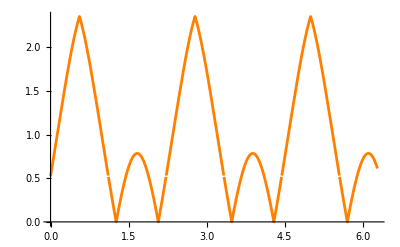

Azimuthal Error Plot (Max):

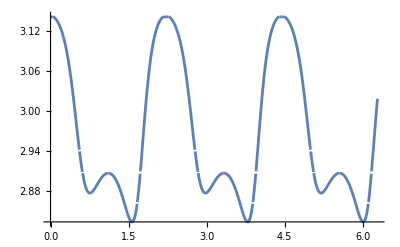

Elevation Error Plot (Min):

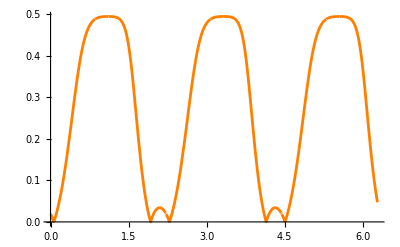

Azimuthal Error Plot (Min):

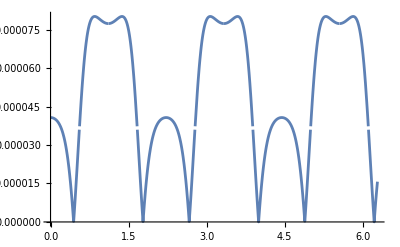

Analyzing Case 4: Irrational ratios

Max Elevation Error: 2.0731745488505802829

Max Azimuthal Error: 3.141592653589768069

Min Elevation Error: 2.1826078194734911042×10^-12

Min Azimuthal Error: 5.4753960043942458876×10^-11

Elevation Error Period: (2 π)/(√(9+6 ⅇ+ⅇ^2+π^2))

Azimuthal Error Period: (2 π)/(√(9+6 ⅇ+ⅇ^2+π^2))

Elevation Error Plot (Max):

-Graphics-

Azimuthal Error Plot (Max):

-Graphics-

Elevation Error Plot (Min):

-Graphics-

Azimuthal Error Plot (Min):

-Graphics-

Analyzing Case 5: Two equal, irrational ratio - Subcase 1

Max Elevation Error: 1.8077146409809789923

Max Azimuthal Error: 3.1415926535660458388

Min Elevation Error: 6.7079499561655997056×10^-11

Min Azimuthal Error: 2.4155815974582619354×10^-10

Elevation Error Period: (2 π)/(√(2+2 π+π^2))

Azimuthal Error Period: (2 π)/(√(2+2 π+π^2))

Elevation Error Plot (Max):

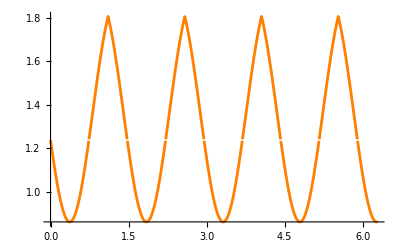

Azimuthal Error Plot (Max):

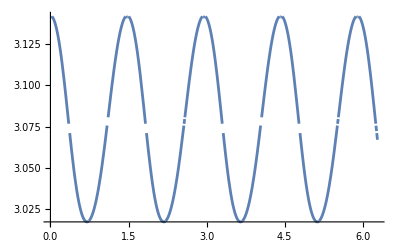

Elevation Error Plot (Min):

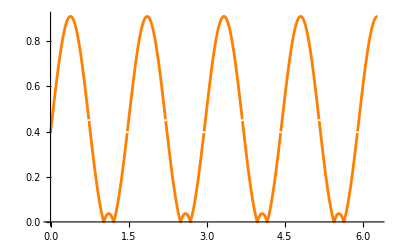

Azimuthal Error Plot (Min):

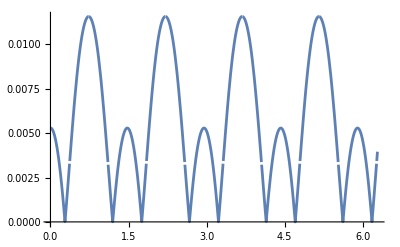

Analyzing Case 5: Two equal, irrational ratio - Subcase 2

Max Elevation Error: 2.5746803090955619695

Max Azimuthal Error: 3.1415926535851332194

Min Elevation Error: 3.8480641613243882253×10^-11

Min Azimuthal Error: 3.4997513983975541756×10^-11

Elevation Error Period: (2 π)/(√(4+π^2))

Azimuthal Error Period: (2 π)/(√(4+π^2))

Elevation Error Plot (Max):

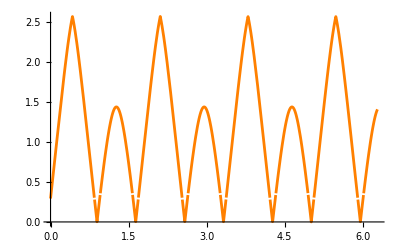

Azimuthal Error Plot (Max):

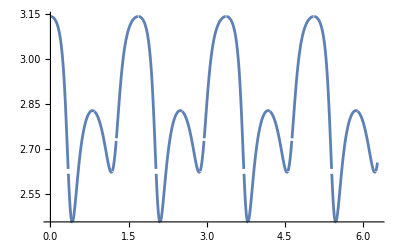

Elevation Error Plot (Min):

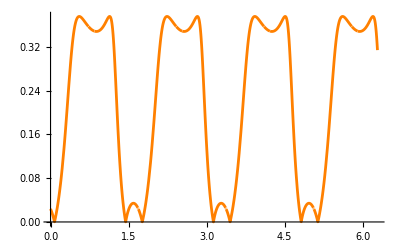

Azimuthal Error Plot (Min):

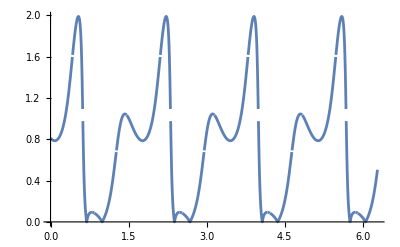

```mathematica
ClearAll["Global`*"];
SetOptions[{NMinimize,NMaximize},WorkingPrecision->20];
subtractAngles[a1_,a2_]:=Module[{d},d=Abs[a1-a2];
Min[d,2*Pi-d]];
SP[t_,θ_,ϕ_,ψ_]:={{Cosh[t Sqrt[-θ^2-(ϕ+ψ)^2]],-((ϕ+ψ) Sinh[t Sqrt[-θ^2-(ϕ+ψ)^2]]/Sqrt[-θ^2-(ϕ+ψ)^2]),(θ Sinh[t Sqrt[-θ^2-(ϕ+ψ)^2]])/Sqrt[-θ^2-(ϕ+ψ)^2]},{((ϕ+ψ) Sinh[t Sqrt[-θ^2-(ϕ+ψ)^2]])/Sqrt[-θ^2-(ϕ+ψ)^2],(θ^2+(ϕ+ψ)^2 Cosh[t Sqrt[-θ^2-(ϕ+ψ)^2]])/(θ^2+(ϕ+ψ)^2),-((θ (ϕ+ψ) (-1+Cosh[t Sqrt[-θ^2-(ϕ+ψ)^2]]))/(θ^2+(ϕ+ψ)^2))},{-((θ Sinh[t Sqrt[-θ^2-(ϕ+ψ)^2]])/Sqrt[-θ^2-(ϕ+ψ)^2]),-((θ (ϕ+ψ) (-1+Cosh[t Sqrt[-θ^2-(ϕ+ψ)^2]]))/(θ^2+(ϕ+ψ)^2)),((ϕ+ψ)^2+θ^2 Cosh[t Sqrt[-θ^2-(ϕ+ψ)^2]])/(θ^2+(ϕ+ψ)^2)}};
angularErrorSimplified[vec_,vecError_,t_,θ_,ϕ_,ψ_,i_]:=Module[{sphericalVec,sphericalVecError},sphericalVec=ToSphericalCoordinates[vec.SP[t,θ,ϕ,ψ]];
sphericalVecError=ToSphericalCoordinates[vecError.SP[t,θ,ϕ,ψ]];
subtractAngles[sphericalVec[[i]],sphericalVecError[[i]]]];
elevationErrorSimplified[errx_,erry_,errz_,t_,θ_,ϕ_,ψ_]:=angularErrorSimplified[{1,0,0},EulerMatrix[{errx,erry,errz}][[1]],t,θ,ϕ,ψ,2];
azimuthalErrorSimplified[errx_,erry_,errz_,t_,θ_,ϕ_,ψ_]:=angularErrorSimplified[{1,0,0},EulerMatrix[{errx,erry,errz}][[1]],t,θ,ϕ,ψ,3];

analyzeCase[θ_,ϕ_,ψ_,caseName_]:=Module[{maxElevation,maxAzimuthal,minElevation,minAzimuthal,maxElevationValues,maxAzimuthalValues,minElevationValues,minAzimuthalValues,elevationPeriod,azimuthalPeriod},Print["Analyzing ",caseName];
maxElevation=NMaximize[{elevationErrorSimplified[x,y,z,t,θ,ϕ,ψ],0<x<2 Pi&&0<y<2 Pi&&0<z<2 Pi&&0<t<2 Pi},{x,y,z,t}];
maxAzimuthal=NMaximize[{azimuthalErrorSimplified[x,y,z,t,θ,ϕ,ψ],0<x<2 Pi&&0<y<2 Pi&&0<z<2 Pi&&0<t<2 Pi},{x,y,z,t}];
minElevation=NMinimize[{elevationErrorSimplified[x,y,z,t,θ,ϕ,ψ],0<x<2 Pi&&0<y<2 Pi&&0<z<2 Pi&&0<t<2 Pi},{x,y,z,t}];
minAzimuthal=NMinimize[{azimuthalErrorSimplified[x,y,z,t,θ,ϕ,ψ],0<x<2 Pi&&0<y<2 Pi&&0<z<2 Pi&&0<t<2 Pi},{x,y,z,t}];
maxElevationValues={x,y,z}/. maxElevation[[2]];
maxAzimuthalValues={x,y,z}/. maxAzimuthal[[2]];
minElevationValues={x,y,z}/. minElevation[[2]];
minAzimuthalValues={x,y,z}/. minAzimuthal[[2]];
elevationPeriod=FunctionPeriod[elevationErrorSimplified[x,y,z,t,θ,ϕ,ψ],t];
azimuthalPeriod=FunctionPeriod[azimuthalErrorSimplified[x,y,z,t,θ,ϕ,ψ],t];
Print["Max Elevation Error: ",maxElevation[[1]]];
Print["Max Azimuthal Error: ",maxAzimuthal[[1]]];
Print["Min Elevation Error: ",minElevation[[1]]];
Print["Min Azimuthal Error: ",minAzimuthal[[1]]];
Print["Elevation Error Period: ",elevationPeriod];
Print["Azimuthal Error Period: ",azimuthalPeriod];
Print["Elevation Error Plot (Max):"];
Print[Plot[elevationErrorSimplified[maxElevationValues[[1]],maxElevationValues[[2]],maxElevationValues[[3]],t,θ,ϕ,ψ],{t,0,2 Pi},PlotRange->All,PlotStyle->Orange]];
Print["Azimuthal Error Plot (Max):"];
Print[Plot[azimuthalErrorSimplified[maxAzimuthalValues[[1]],maxAzimuthalValues[[2]],maxAzimuthalValues[[3]],t,θ,ϕ,ψ],{t,0,2 Pi},PlotRange->All]];
Print["Elevation Error Plot (Min):"];
Print[Plot[elevationErrorSimplified[minElevationValues[[1]],minElevationValues[[2]],minElevationValues[[3]],t,θ,ϕ,ψ],{t,0,2 Pi},PlotRange->All,PlotStyle->Orange]];
Print["Azimuthal Error Plot (Min):"];
Print[Plot[azimuthalErrorSimplified[minAzimuthalValues[[1]],minAzimuthalValues[[2]],minAzimuthalValues[[3]],t,θ,ϕ,ψ],{t,0,2 Pi},PlotRange->All]];
Print["\n"];];

analyzeCase[Pi/100,Pi/100,Pi/100,"Case 1: All equal"];
analyzeCase[Pi/100,Pi/200,Pi/300,"Case 2: Rational ratios"];
analyzeCase[Pi/100,Pi/100,Pi/200,"Case 3: Two equal, rational ratio"];
analyzeCase[Pi,E,3,"Case 4: Irrational ratios"];
analyzeCase[Pi/100,Pi/100,E,"Case 5: Two equal, irrational ratio"];

analyzeCase[1,1,1,"Case 1: All equal - Eldar's Case"];
analyzeCase[1,2,3,"Case 2: Rational ratios - Subcase 1"];
analyzeCase[3,2,1,"Case 2: Rational ratios - Subcase 2"];
analyzeCase[1,1,2,"Case 3: Two equal, rational ratio - Subcase 1"];
analyzeCase[2,1,1,"Case 3: Two equal, rational ratio - Subcase 2"];
analyzeCase[Pi,E,3,"Case 4: Irrational ratios"];
(*analyzeCase[1,1,E,"Case 5: Two equal, irrational ratio"];*)
analyzeCase[1,1,Pi,"Case 5: Two equal, irrational ratio - Subcase 1"];
analyzeCase[Pi,1,1,"Case 5: Two equal, irrational ratio - Subcase 2"];
```